```mathematica
Import["ToMatlab.m","Package"]
```

# Supporting Information Sec 3.1 p=1, triangular flake shape, based on -Graphics-

## AA stacking. Considering moire rotation Eq. S1

```mathematica
ClearAll["Global`*"]
```

```mathematica
$Assumptions=R>0 && c>0 && 0≤θ ≤ Pi/3  &&n ∈ Integers && Kx∈ Reals &&Ky ∈ Reals && xl∈ Reals &&yl∈ Reals && dmx∈ Reals &&dmy∈ Reals  &&c>0 && A>0   && l∈ Integers && λ>0 && x ∈ Reals && y ∈ Reals && as>0 && cs>0 &&r>0 && theta>0 && theta≤10/180*Pi
```

R>0&&c>0&&0≤θ≤π/3&&n∈ℤ&&Kx∈ℝ&&Ky∈ℝ&&xl∈ℝ&&yl∈ℝ&&dmx∈ℝ&&dmy∈ℝ&&c>0&&A>0&&l∈ℤ&&λ>0&&x∈ℝ&&y∈ℝ&&as>0&&cs>0&&r>0&&theta>0&&theta≤π/18

```mathematica
fAA[x_,y_,λ_]=  Cos[(4 π x)/(√3 λ)]+2 Cos[(2  π x)/(√3 λ)] Cos[(2  π y)/λ]
```

Cos[(4 π x)/(√3 λ)]+2 Cos[(2 π x)/(√3 λ)] Cos[(2 π y)/λ]

```mathematica
Plot3D[fAA[x,y,1],{x,-2,2},{y,-2,2},AxesLabel->Automatic,ViewPoint->{0,0,Infinity}, ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
fthetaAA[x_,y_,λ_,θ_]=fAA[x Cos[θ/2]-y Sin[θ/2],y Cos[θ/2]+x Sin[θ/2],λ] 
(*Rotate counter-clockwise*)
```

2 Cos[(2 π (y Cos[θ/2]+x Sin[θ/2]))/λ] Cos[(2 π (x Cos[θ/2]-y Sin[θ/2]))/(√3 λ)]+Cos[(4 π (x Cos[θ/2]-y Sin[θ/2]))/(√3 λ)]

```mathematica
λ0=as/(2*(1-Cos[θ]))^(1/2)
```

as/(√2 √(1-Cos[θ]))

```mathematica
f0AA[x_,y_,as_,θ_]=Simplify[fthetaAA[x,y,λ0,θ]]
```

2 Cos[(2 π √(2-2 Cos[θ]) (y Cos[θ/2]+x Sin[θ/2]))/as] Cos[(2 π √(6-6 Cos[θ]) (x Cos[θ/2]-y Sin[θ/2]))/(3 as)]+Cos[(4 π √(6-6 Cos[θ]) (x Cos[θ/2]-y Sin[θ/2]))/(3 as)]

```mathematica
nRf0AA[x_,y_,as_,θ_,R_]=f0AA[x R,y R,as,θ]
```

2 Cos[(2 π √(2-2 Cos[θ]) (R y Cos[θ/2]+R x Sin[θ/2]))/as] Cos[(2 π √(6-6 Cos[θ]) (R x Cos[θ/2]-R y Sin[θ/2]))/(3 as)]+Cos[(4 π √(6-6 Cos[θ]) (R x Cos[θ/2]-R y Sin[θ/2]))/(3 as)]

```mathematica
nRnasf0AA[x_,y_,as_,θ_,r_]=Simplify[nRf0AA[x,y,as,θ,r*as]]
```

Sin[1/6 π (3-8 r √(6-6 Cos[θ]) (x Cos[θ/2]-y Sin[θ/2]))]+2 Cos[2 π r √(2-2 Cos[θ]) (y Cos[θ/2]+x Sin[θ/2])] Sin[1/6 π (3-4 r √(6-6 Cos[θ]) (x Cos[θ/2]-y Sin[θ/2]))]

```mathematica
nRnasnareauf0AA[x_,y_,θ_,r_]=Simplify[nRnasf0AA[x,y,as,θ,r]]
```

Sin[1/6 π (3-8 r √(6-6 Cos[θ]) (x Cos[θ/2]-y Sin[θ/2]))]+2 Cos[2 π r √(2-2 Cos[θ]) (y Cos[θ/2]+x Sin[θ/2])] Sin[1/6 π (3-4 r √(6-6 Cos[θ]) (x Cos[θ/2]-y Sin[θ/2]))]

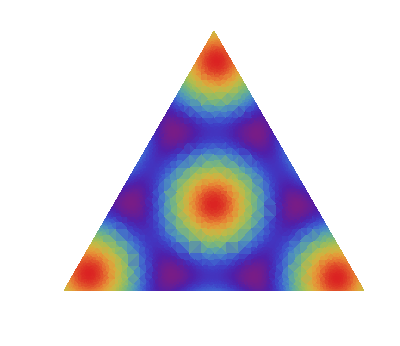

```mathematica
DensityPlot[nRnasnareauf0AA[x,y,2/180*Pi,20Sqrt[3]],{x,-1,1},{y,-1,1},AxesLabel->Automatic, ColorFunction->"Rainbow",MaxRecursion->3, PlotRange->All,RegionFunction->Function[{x,y,z},y+Sqrt[3]x<1 &&y<Sqrt[3]x+1&& y>-1/2],AspectRatio->Automatic,Frame->False,FrameTicks->False]
```

```mathematica
triarea=Integrate[Boole[y+Sqrt[3]x<1 &&y<Sqrt[3]x+1&& y>-1/2],{x,-1,1},{y,-1,1}]
```

(3 √3)/4

```mathematica
t1=AbsoluteTime[];
AAtri1[theta_,r_]=FullSimplify[Integrate[nRnasnareauf0AA[x,y,theta,r]Boole[y+Sqrt[3]x<1 &&y<Sqrt[3]x+1&& y>-1/2],{x,-1,1},{y,-1,1}] ]
t2=AbsoluteTime[];
Print["time used ",(t2-t1)/60," mins" ]
```

-((9 (1+2 Cos[theta]) Csc[theta/2]^3 Sec[theta/2] (-2 √3 Cos[(4 π r (-1+Cos[theta]))/(√3)] Sin[theta]+Cos[2/3 π r (√3-√3 Cos[theta]+3 Sin[theta])] (-3+√3 Sin[theta])+Cos[2/3 π r (√3-√3 Cos[theta]-3 Sin[theta])] (3+√3 Sin[theta])+6 Cos[theta] Sin[(2 π r (-1+Cos[theta]))/(√3)] Sin[2 π r Sin[theta]]))/(128 π^2 r^2 (1+2 Cos[2 theta])))

time used 4.60930695 mins

```mathematica
AAtri[θ_,r_]=FullSimplify[AAtri1[θ,r]/triarea ]
```

-1/(32 π^2 r^2 (1+2 Cos[2 θ]))3 (1+2 Cos[θ]) Csc[θ/2]^3 Sec[θ/2] (-2 Cos[(4 π r (-1+Cos[θ]))/(√3)] Sin[θ]+Cos[2/3 π r (√3-√3 Cos[θ]+3 Sin[θ])] (-√3+Sin[θ])+Cos[2/3 π r (√3-√3 Cos[θ]-3 Sin[θ])] (√3+Sin[θ])+2 √3 Cos[θ] Sin[(2 π r (-1+Cos[θ]))/(√3)] Sin[2 π r Sin[θ]])

```mathematica
ToMatlab[AAtri[theta,r]]
```

(-3/32).*pi.^(-2).*r.^(-2).*(1+2.*cos(theta)).*(1+2.*cos(2.*theta) ...
  ).^(-1).*csc((1/2).*theta).^3.*sec((1/2).*theta).*((-2).*cos(4.* ...
  3.^(-1/2).*pi.*r.*((-1)+cos(theta))).*sin(theta)+cos((2/3).*pi.* ...
  r.*(3.^(1/2)+(-1).*3.^(1/2).*cos(theta)+3.*sin(theta))).*((-1).* ...
  3.^(1/2)+sin(theta))+cos((2/3).*pi.*r.*(3.^(1/2)+(-1).*3.^(1/2).* ...
  cos(theta)+(-3).*sin(theta))).*(3.^(1/2)+sin(theta))+2.*3.^(1/2).* ...
  cos(theta).*sin(2.*3.^(-1/2).*pi.*r.*((-1)+cos(theta))).*sin(2.* ...
  pi.*r.*sin(theta)));

## AB stacking. Considering moire rotation Eq. S2

```mathematica
ClearAll["Global`*"]
```

```mathematica
$Assumptions=R>0 && c>0 && 0≤θ ≤ Pi/3  &&n ∈ Integers && Kx∈ Reals &&Ky ∈ Reals && xl∈ Reals &&yl∈ Reals && dmx∈ Reals &&dmy∈ Reals  &&c>0 && A>0   && l∈ Integers && λ>0 && x ∈ Reals && y ∈ Reals && as>0 && cs>0 &&r>0 && theta>0 && theta≤10/180*Pi
```

R>0&&c>0&&0≤θ≤π/3&&n∈ℤ&&Kx∈ℝ&&Ky∈ℝ&&xl∈ℝ&&yl∈ℝ&&dmx∈ℝ&&dmy∈ℝ&&c>0&&A>0&&l∈ℤ&&λ>0&&x∈ℝ&&y∈ℝ&&as>0&&cs>0&&r>0&&theta>0&&theta≤π/18

```mathematica
fAB[x_,y_,λ_]=Cos[(4 π (x-λ/√3))/(√3 λ)]+2 Cos[(2  π (x-λ/√3))/(√3 λ)] Cos[(2  π y)/λ]
```

2 Cos[(2 π y)/λ] Cos[(2 π (x-λ/(√3)))/(√3 λ)]+Cos[(4 π (x-λ/(√3)))/(√3 λ)]

```mathematica
Plot3D[fAB[x,y,1],{x,-2,2},{y,-2,2},AxesLabel->Automatic,ViewPoint->{0,0,Infinity}, ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
fthetaAB[x_,y_,λ_,θ_]=fAB[x Cos[θ/2]-y Sin[θ/2],y Cos[θ/2]+x Sin[θ/2],λ] 
(*Rotate counter-clockwise*)
```

2 Cos[(2 π (y Cos[θ/2]+x Sin[θ/2]))/λ] Cos[(2 π (-λ/(√3)+x Cos[θ/2]-y Sin[θ/2]))/(√3 λ)]+Cos[(4 π (-λ/(√3)+x Cos[θ/2]-y Sin[θ/2]))/(√3 λ)]

```mathematica
λ0=as/(2*(1-Cos[θ]))^(1/2)
```

as/(√2 √(1-Cos[θ]))

```mathematica
f0AB[x_,y_,as_,θ_]=Simplify[fthetaAB[x,y,λ0,θ]]
```

2 Cos[(2 π √(2-2 Cos[θ]) (y Cos[θ/2]+x Sin[θ/2]))/as] Cos[(2 π (as-x Cos[θ/2] √(6-6 Cos[θ])+y √(6-6 Cos[θ]) Sin[θ/2]))/(3 as)]+Cos[(4 π (as-x Cos[θ/2] √(6-6 Cos[θ])+y √(6-6 Cos[θ]) Sin[θ/2]))/(3 as)]

```mathematica
nRf0AB[x_,y_,as_,θ_,R_]=f0AB[x R,y R,as,θ]
```

2 Cos[(2 π √(2-2 Cos[θ]) (R y Cos[θ/2]+R x Sin[θ/2]))/as] Cos[(2 π (as-R x Cos[θ/2] √(6-6 Cos[θ])+R y √(6-6 Cos[θ]) Sin[θ/2]))/(3 as)]+Cos[(4 π (as-R x Cos[θ/2] √(6-6 Cos[θ])+R y √(6-6 Cos[θ]) Sin[θ/2]))/(3 as)]

```mathematica
nRnasf0AB[x_,y_,as_,θ_,r_]=Simplify[nRf0AB[x,y,as,θ,r*as]]
```

2 Cos[2 π r √(2-2 Cos[θ]) (y Cos[θ/2]+x Sin[θ/2])] Cos[2/3 π (-1+r x Cos[θ/2] √(6-6 Cos[θ])-r y √(6-6 Cos[θ]) Sin[θ/2])]+Cos[4/3 π (-1+r x Cos[θ/2] √(6-6 Cos[θ])-r y √(6-6 Cos[θ]) Sin[θ/2])]

```mathematica
nRnasnareauf0AB[x_,y_,θ_,r_]=Simplify[nRnasf0AB[x,y,as,θ,r]]
```

2 Cos[2 π r √(2-2 Cos[θ]) (y Cos[θ/2]+x Sin[θ/2])] Cos[2/3 π (-1+r x Cos[θ/2] √(6-6 Cos[θ])-r y √(6-6 Cos[θ]) Sin[θ/2])]+Cos[4/3 π (-1+r x Cos[θ/2] √(6-6 Cos[θ])-r y √(6-6 Cos[θ]) Sin[θ/2])]

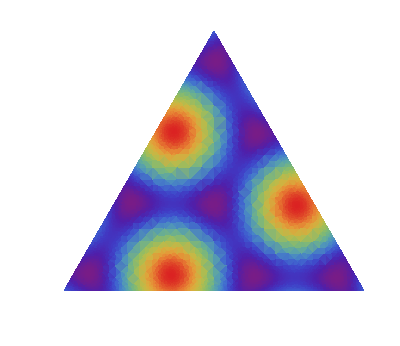

```mathematica
DensityPlot[nRnasnareauf0AB[x,y,2/180*Pi,20Sqrt[3]],{x,-1,1},{y,-1,1},AxesLabel->Automatic, ColorFunction->"Rainbow",MaxRecursion->3, PlotRange->All,RegionFunction->Function[{x,y,z},y+Sqrt[3]x<1 &&y<Sqrt[3]x+1&& y>-1/2],AspectRatio->Automatic,Frame->False,FrameTicks->False]
```

```mathematica
triarea=Integrate[Boole[y+Sqrt[3]x<1 &&y<Sqrt[3]x+1&& y>-1/2],{x,-1,1},{y,-1,1}]
```

(3 √3)/4

```mathematica
t1=AbsoluteTime[];
ABtri[theta_,r_]=FullSimplify[Integrate[nRnasnareauf0AB[x,y,theta,r]Boole[y+Sqrt[3]x<1 &&y<Sqrt[3]x+1&& y>-1/2],{x,-1,1},{y,-1,1}] /triarea]
t2=AbsoluteTime[];
Print["time used ",(t2-t1)/60," mins" ]
```

(3 Csc[theta/2]^2 Sin[(3 theta)/2] (Cos[1/3 π (1-2 √3 r+2 √3 r Cos[theta]+6 r Sin[theta])] (Csc[theta/2]+√3 Sec[theta/2])-2 Csc[theta/2] Sin[1/6 π (1+8 √3 r (-1+Cos[theta]))]+(Csc[theta/2]-√3 Sec[theta/2]) Sin[1/6 π (1-4 √3 r Cos[theta]+4 r (√3+3 Sin[theta]))]))/(16 π^2 r^2 (1+2 Cos[2 theta]))

time used 10.1572562 mins

```mathematica
ABtri[θ,r]
```

1/(16 π^2 r^2 (1+2 Cos[2 θ]))3 Csc[θ/2]^2 Sin[(3 θ)/2] (Cos[1/3 π (1-2 √3 r+2 √3 r Cos[θ]+6 r Sin[θ])] (Csc[θ/2]+√3 Sec[θ/2])-2 Csc[θ/2] Sin[1/6 π (1+8 √3 r (-1+Cos[θ]))]+(Csc[θ/2]-√3 Sec[θ/2]) Sin[1/6 π (1-4 √3 r Cos[θ]+4 r (√3+3 Sin[θ]))])

```mathematica
ToMatlab[ABtri[theta,r]]
```

(3/16).*pi.^(-2).*r.^(-2).*(1+2.*cos(2.*theta)).^(-1).*csc((1/2).* ...
  theta).^2.*sin((3/2).*theta).*(cos((1/3).*pi.*(1+(-2).*3.^(1/2).* ...
  r+2.*3.^(1/2).*r.*cos(theta)+6.*r.*sin(theta))).*(csc((1/2).* ...
  theta)+3.^(1/2).*sec((1/2).*theta))+(-2).*csc((1/2).*theta).*sin(( ...
  1/6).*pi.*(1+8.*3.^(1/2).*r.*((-1)+cos(theta))))+(csc((1/2).* ...
  theta)+(-1).*3.^(1/2).*sec((1/2).*theta)).*sin((1/6).*pi.*(1+(-4) ...
  .*3.^(1/2).*r.*cos(theta)+4.*r.*(3.^(1/2)+3.*sin(theta)))));